In biology there are patterns of life that grow infinitely and uncontrollably (such as tumors), other that die out immediately under certain conditions and some other that persists for only a finite number of steps. Interestingly, some cellular automaton rules exhibit the similar behaviour. This work explore such rules within the context  of one-dimensional totalistic cellular automata, focusing of those that generate finite life when starting from a single cell active.

## Introduction

Cellular Automata (CA) are simple mathematical systems that evolve in discrete steps, where each cell in a grid updates its state based on a set of rules and the states of its neighbours. Despite their simplicity, they can produce surprisingly complex behaviour and have been widely studied in areas such as mathematics, physics, computer science, and biology.

Among the different types of behaviour that can emerge from cellular automata, one especially interesting case is that of finite lifeforms. These are patterns that, starting from a single active cell, grow for a certain number of steps before stopping completely. They don’t disappear instantly, but they also don’t expand forever. This behaviour can be compared to some biological processes that are active for a limited time, like certain types of cell growth.

This project explores totalistic cellular automata in one dimension — a class where the rules depend only on the total sum of neighbouring cell states. Through a series of filters and computational tools, we reduce the number of possible rules and identify which ones can generate finite lifeforms. We also analyse how these rules relate to each other by building graphs that connect similar behaviours.

Since testing all possible rules is computationally expensive, we also designed an algorithm that discovers new rules by applying small changes (mutations) to existing ones. This strategy helps to explore the space of rules more efficiently and understand the structure behind these finite lifeform patterns.

## Theoretical framework

### Definitions

#### Cellular Automata

Cellular automata (CA) are defined as a collection of cells arranged in a regular grid, where each cell updates its value based on the interaction with its neighbors. Mathematically, a cellular automaton is described by a 4-tuple:

L: The dimensional space. It defines the dimensionality of the grid of cells. This space is (theoretically) infinite.

S: A finite set of possible states that each cell can assume within the assigned space.

N: The neighborhood. It defines the relative positions of the cells that make up each cell’s neighborhood. The behavior of each cell depends on the states of its neighbors.

f: The transition function, defined as . It determines the next state of each cell based on the states of its neighbors. This update occurs simultaneously for all cells at each discrete time step.

#### Elementary Cellular Automata

Elementary Cellular Automata (ECA) represent the simplest class of cellular automata. Their characteristics are as follows:

L = 1: The cell are arranged in a  one-dimensional consecutive infinite line.

S = {0, 1}: Each cell can be in one of two possible states.

N = {-1, 0, 1}: The neighborhood consists of the cell itself and its two immediate neighbors, one to the left and one to the right. This is also referred to as radius 1.

The transition function depends on the states of three cells, and since each cell can be in one of two states, there are  possible neighborhood configurations. Each of these 8 configurations can map to either 0 or 1 as the next state, which gives us a total of   different elementary cellular automaton rules.

Each rule can be uniquely identified by the binary output assigned to the 8 neighborhood configurations. This binary number can be interpreted as a decimal value between 0 and 255. For example, the rule corresponding to the binary sequence 11010010 is known as Rule 210, since  .

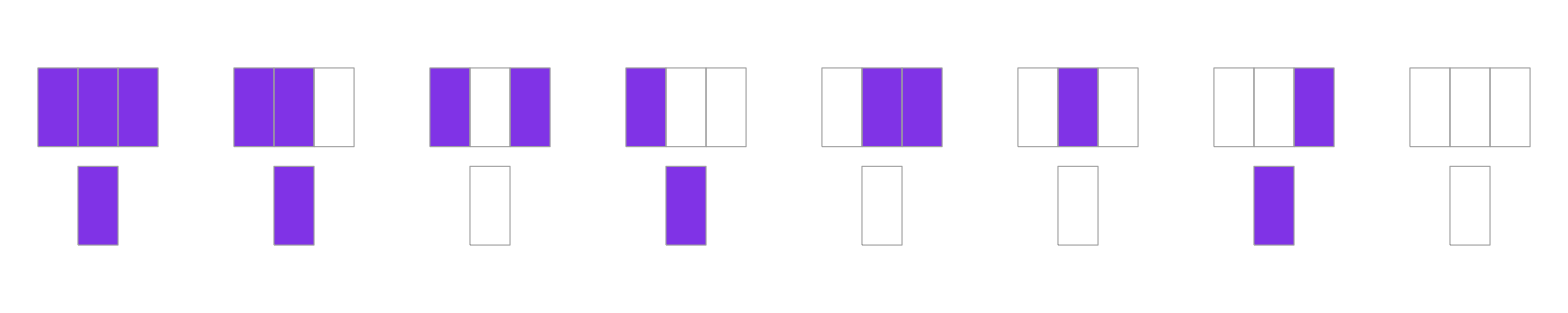
-Graphics-ECA 210

```mathematica
Labeled[RulePlot[CellularAutomaton[210],ColorRules->globalColorRules],Style[Text["ECA 210"],12]]
```

The figure below illustrates this rule, where black squares represent state 1 and white squares represent state 0.

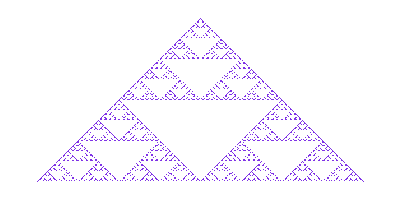
-Graphics-Evolution of ECA 210

```mathematica
Labeled[ArrayPlot[CellularAutomaton[210,{{1},0},256],ColorRules->globalColorRules],Style[Text["Evolution of ECA 210"],12]]
```

#### Totalistic Cellular Automata

Totalistic Cellular Automata (TCA) are a type of cellular automaton in which the transition rules depend solely on the sum (or equivalently, the average) of the values of the cells in a neighborhood. Although TCAs can be described using standard cellular automaton formalisms, this formulation significantly reduces the number of possible rules.

This type of rule is used, for example, in Conway' s Game of Life .

The evolution of a one - dimensional totalistic cellular automaton is illustrated in the following figure.

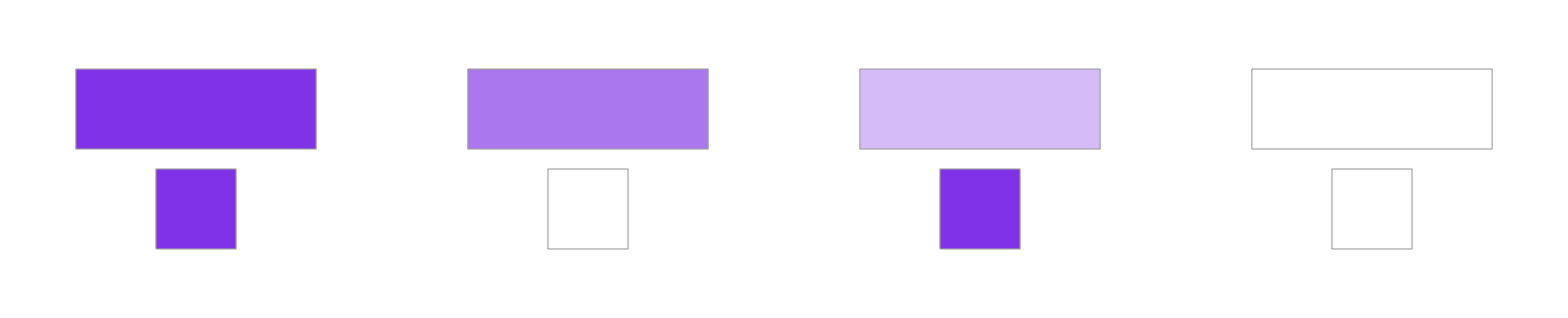
-Graphics-TCA 20

```mathematica
Labeled[RulePlot[CellularAutomaton[{10,{2,1},1}],ColorRules->globalColorRules],Style[Text["TCA 20"],12]]
```

The evolution of a one-dimensional cellular automaton is illustrated in the next figure.

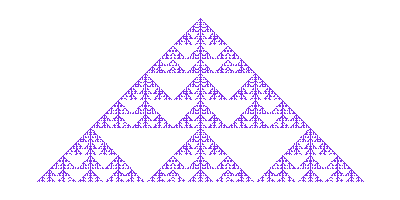
-Graphics-Evolution of TCA 10

```mathematica
Labeled[ArrayPlot[CellularAutomaton[{10,{2,1},1},{{1},0},190],ColorRules->globalColorRules],Style[Text["Evolution of TCA 10"],12]]
```

#### Finite lifeforms

Starting from a single active cell, there are certain rules that produce patterns with finite lifespans, that is, their evolution is neither infinite nor does it die out immediately. These patterns persist for a limited number of time steps before becoming inactive.

The following example involves a system with three states, and its evolution is shown in the next figure.

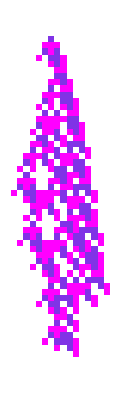
-Graphics-Rule 5600111605818 (3 states)

```mathematica
Labeled[ArrayPlot[CellularAutomaton[{5600111605818,3,1},{{1},0},52],
ColorRules->globalColorRules],Style[Text["Rule 5600111605818 (3 states)"],12]]
```

This behaviour can be  also found in TCA. For example, the next figure shows the finite lifetime of the rule 357 (3 states) which lives exactly 87 steps.

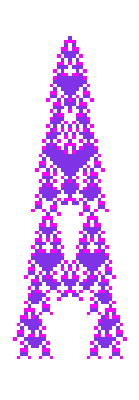

```mathematica
ArrayPlot[CellularAutomaton[{357,{3,1},1},{{1},0},88],ColorRules->globalColorRules]
```

## Brute force search

The total number of TCA rules is given by the following formula:

Where:

is the number of possible states per cell

r is the neighborhood radius

This formula accounts for all possible totalistic transition functions.

### Filtering totalistic rules

The number of TCA rules increases exponentially with the number of states. For this reason, it is necessary to apply a series of filters to reduce the search space.

#### Spontaneous Life

Rules that generate activity from an entirely inactive neighborhood (i.e., where the sum is zero) are considered to produce spontaneous life. These are discarded by checking if the transition function assigns a non-zero value to the lowest input sum (the last position in the rule vector).

```mathematica
Import["./img/spontaneous_life.gif","AnimatedImage"]
```

#### Infinite Growth

The second filter considers the initial condition. If the output in the rule’s second position is the same as the initial cell’s state, the pattern will grow indefinitely. These rules are also excluded.

```mathematica
(*Vista previa*)
Import["./img/spontaneous_life_k3.gif","AnimatedImage"]
```

#### Spontaneous Death

The third filter involves applying the CellularAutomaton function for a single time step to remove rules that cause the pattern to vanish immediately, i.e., those that lead to spontaneous death.

```mathematica
Import["./img/filtered_rules_k"<>ToString[k]<>"_r"<>ToString[r]<>".gif","AnimatedImage"]
```

### Configurations

By applying the proposed filters, the number of TCA rules is significantly reduced, enough to allow a brute-force search for finite lifeforms. Unfortunately, brute-force methods are only feasible for rule sets below approximately 2 million entries. Beyond this threshold, the computational cost becomes inefficient.

The following table summarizes the total number of rules and the number of rules remaining after filtering, for different combinations of state count 𝑘 and neighborhood radius 𝑟:

```mathematica
configurations={
<|"k"->2,"r"->1/2,"rules"->7,"filtered"->0|>,
<|"k"->3,"r"->1/2,"rules"->242,"filtered"->27|>,
<|"k"->4,"r"->1/2,"rules"->16383,"filtered"->2048|>,
<|"k"->5,"r"->1/2,"rules"->1953124,"filtered"->234375|>,
<|"k"->2,"r"->1,"rules"->15,"filtered"->0|>,
<|"k"->3,"r"->1,"rules"->2186,"filtered"->243|>,
<|"k"->4,"r"->1,"rules"->1048575,"filtered"->131072|>,
<|"k"->2,"r"->2,"rules"->63,"filtered"->0|>,
<|"k"->3,"r"->2,"rules"->177146,"filtered"->19683|>,
<|"k"->2,"r"->3/2,"rules"->31,"filtered"->0|>,
<|"k"->3,"r"->3/2,"rules"->19682,"filtered"->2187|>,
<|"k"->2,"r"->3,"rules"->255,"filtered"->0|>,
<|"k"->2,"r"->5/2,"rules"->127,"filtered"->0|>,
<|"k"->3,"r"->5/2,"rules"->1594322,"filtered"->177147|>
};
configurations=SortBy[configurations,#["filtered"]&];
configurations//Dataset
configurations=Select[configurations,#["filtered"]>0&];
```

### Execution

The following iconized object contains all the different rules that produce finite lifeforms, grouped by the same resulting pattern. Each group is generated from all possible initial states (20 configurations in total).

```mathematica
configRules=;
```

The animations below display all the finite lifeforms corresponding to the first 6 configurations mentioned above. Generally, the smaller the finite lifeform, the greater the number of rules capable of producing that pattern.

In some configurations, the displayed rule includes elements in the rule vector marked with an ‘’. This symbol indicates that the value at that position can be arbitrary, any value will lead to the same resulting pattern.

```mathematica
SetDirectory[NotebookDirectory[]];
gifs=Table[Import["./gif/"<>ToString[i]<>"_loop.gif","AnimatedImage"]//ImageResize[#,{430}]&,{i,4,9}];

GraphicsGrid[Partition[gifs,3],Spacings->{0,0},Frame->None,ImageSize->{1200}]
```

-Graphics-

Below are the best rules found across different configurations.

The longest finite lifeform discovered through brute-force search was of length 109,521, using parameters  k = 3, r = 2.5, initial states of 2 and a grid of length 699.

```mathematica
SetDirectory[NotebookDirectory[]];
clean=configRules[[;;,{"k","r","init","groups"}]];
separated=Flatten[Table[
Table[
{
c[["k"]],
c[["r"]],
c[["init"]],
group[["length"]]
,group[["rules"]]
},{group,c[["groups"]]}]
,{c,clean}],1];
rules=SortBy[separated,#[[4]]&][[-10;;]][[All]];

imageList=Table[Import[FileNameJoin[{"best","tca_"<>ToString[i]<>".png"}]],{i,1,10}];

labeledImages=Table[Labeled[imageList[[i]],Style[Text[Column[{Style["k: "<>ToString[rules[[i,1]]],Bold,14],"r: "<>ToString[N[rules[[i,2]]]],"init: "<>ToString[rules[[i,3]]],"length: "<>ToString[rules[[i,4]]],"rule: "<>ToString[rules[[i,5,1]]]},Spacings->0.2]],12],Bottom],{i,Length[imageList]}];

Print[Row[labeledImages]]
```

-Graphics-

The 3D plot below displays all discovered rules under 700 steps for the same configuration.

The height of each node represents the scaled length of the lifeform.

Edges indicate that one rule can be transformed into another via a single mutation in the rule vector.

A common pattern observed across all graphs is that longer lifeforms tend to have fewer connections . This sparsity in connectivity makes random walks a poor strategy for discovering long finite lifeforms, as the probability of reaching high-scoring configurations becomes significantly lower.

```mathematica
graph=Draw3D[configRules[[16,"groups"]]];
```

-Graphics3D-

The following graph shows that shorter lifeforms can be produced by a larger number of rules, while longer lifeforms are generated by fewer rules. This inverse relationship highlights how complex patterns are rarer and require more specific rule configurations.

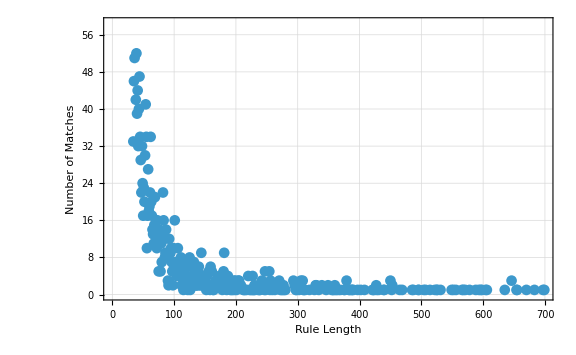

```mathematica
grouped=GroupBy[separated,#[[4]]&];
keys=grouped//Keys;
ListPlot[Table[{k,grouped[k][[All,5]]//Flatten//Length},{k,keys}],PlotStyle->Directive[globalColorRules[6],PointSize[Medium]],AxesLabel->{"Lifetime Length","Number of Matches"},LabelStyle->{FontFamily->"Helvetica",FontSize->14},PlotMarkers->Automatic,GridLines->Automatic,PlotTheme->"Detailed",ImageSize->Large,Frame->True,FrameLabel->{"Rule Length","Number of Matches"},FrameTicks->Automatic]
```

## Graph build and search

The generated graphs for each configuration reveal that there are direct connections between all rules that produce finite lifeforms. However, since the total number of rules grows exponentially with the number of states and neighbourhood radius, it becomes computationally infeasible to exhaustively test all configurations, even after applying the filtering strategies.

For this reason, the following algorithm is designed to discover rule-to-rule relationships by starting from a random rule and iteratively applying mutations to its rule vector. This process builds a graph that captures the local structure of rule space, highlighting how small changes can lead from one finite lifeform-producing rule to another.

First, is necessary to define the configuration, those are the number of states, the radius of the neighbourhood, the initial cell and the number of unique finite lifeforms to search.

```mathematica
k=3;
r=1;
init=1;
graph=Graph[BreadthFirstGroup[k,r,init,-1]];
```

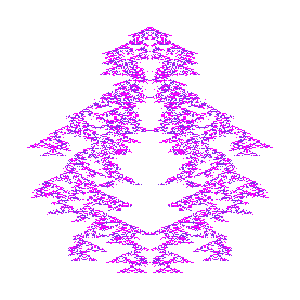
-Graphics-rule:167703
length: 654
k: 3
r:2
init:1

```mathematica
best=Reverse[SortBy[VertexList[graph],#[["length"]]&]][[1]];
Labeled[
DrawCA[CellularAutomaton[{best[["rules",1]],{k,1},r},{{init},0},best[["length"]]],k],
"rule:"<>ToString[best[["rules",1]]]<>"\nlength: "<>ToString[best[["length"]]]<>"\nk: "<>ToString[k]<>"\nr:"<>ToString[r]<>"\ninit:"<>ToString[init],
Right
]
```

The following algorithm implements a breadth-first search strategy to explore the space of totalistic cellular automata (TCA) rules that produce finite lifeforms . The process starts from the null rule, which is guaranteed to mutate into a valid finite lifeform with a single change.

Once the first finite lifeform is found, its neighboring rules (i.e., those reachable through a single mutation) are collected. For each neighbor, the algorithm determines whether it produces the same evolution (same pattern and same lifetime). If so, the rule is grouped together with its equivalent class, and all of its neighbors are added to the search frontier (toTest).
If the rule produces a new, distinct lifeform, it is either assigned to an existing group (if it matches an existing pattern) or used to create a new group.

At each iteration:

New connections (edges) are created between the current node and its neighboring nodes.

The algorithm continues expanding until the specified depth (i.e., number of nodes visited) is reached.

This strategy avoids redundant pattern checks and reveals how small mutations lead to connected components of rules producing similar finite patterns.

```mathematica
BreadthFirstGroup[k_,r_,init_,depth_]:=Module[{visitedRules={},(*List of visited rules*)
nodes={},(*List of discovered nodes*)
edges={},(*List of edges (connections) between nodes*)pendingPositions={},    (*Temporary positions to build edges*)
finiteNeighbors,similarRules,currentNodeIndex,toTestIndex,foundNode,neighborsToAdd
},

(*Start from the null rule*)
rule={0,0};
finiteNeighbors=ClassifyNeighbourRules[rule[[1]],k,r][[3]];
similarRules={};

(*Create the initial node and add it to nodes*)node=<|"rules"->Append[similarRules,rule[[1]]],"length"->rule[[2]]|>;
AppendTo[nodes,node];
currentNodeIndex=0;
(*Iterate until all nodes are visited or depth limit is reached*)
Monitor[While[currentNodeIndex<Length[nodes],currentNodeIndex++;
node=nodes[[currentNodeIndex]];

(*Add all rules in the current node to the visited list*)
visitedRules=Join[visitedRules,node["rules"]]//Flatten;

(*Generate a list of neighbor rules not yet visited*)
toTest=Select[Join[Flatten[Table[finiteNeighbors=ClassifyNeighbourRules[rule,k,r][[3]],{rule,node["rules"]}],1],Select[finiteNeighbors,Not[MemberQ[similarRules,#]]&]]//DeleteDuplicates,Not[MemberQ[visitedRules,#[[1]]]]&];

(*Mark these new rules as visited*)
visitedRules=Join[visitedRules,toTest[[All,1]]];

(*Explore each candidate rule*)toTestIndex=0;
Monitor[While[toTestIndex<Length[toTest],toTestIndex++;
rule=toTest[[toTestIndex]];

(*Find existing nodes with the same pattern length*)possibleNodes=Select[nodes,#["length"]==rule[[2]]&];

(*Check if the rule has the same evolution as any existing node*)foundNode=Select[possibleNodes,(CellularAutomaton[{#[["rules",1]],{k,1},r},{{init},0},rule[[2]]-1]==CellularAutomaton[{rule[[1]],{k,1},r},{{init},0},rule[[2]]-1])&];

(*If no matching node found,create a new one*)If[Length[foundNode]==0,newNode=<|"rules"->{rule[[1]]},"length"->rule[[2]],"rule"->IntegerDigits[rule[[1]],k,RuleLength[k,r]]|>;
AppendTo[nodes,newNode];
AppendTo[pendingPositions,Length[nodes]],

(*Otherwise add the rule to the existing node*)addPos=Position[nodes,foundNode[[1]]][[1,1]];
AppendTo[pendingPositions,addPos];

(*If the node found is the current node, add its neighbors to toTest*)If[addPos==currentNodeIndex,neighborsToAdd=Select[ClassifyNeighbourRules[rule[[1]],k,r][[3]],Not[MemberQ[visitedRules,#[[1]]]]&];
visitedRules=Join[visitedRules,neighborsToAdd[[All,1]]];
toTest=Join[toTest,neighborsToAdd];];
AppendTo[nodes[[addPos,"rules"]],rule[[1]]];];],ProgressIndicator[toTestIndex,{0,Length[toTest]}]];

(*Remove duplicates and current node from positions*)pendingPositions=DeleteCases[pendingPositions//DeleteDuplicates,currentNodeIndex];

(*Create edges (connections) between current node and discovered nodes*)edges=Join[edges,Table[{currentNodeIndex,pos},{pos,pendingPositions}]];

(*Stop if depth limit is reached*)If[currentNodeIndex==depth,Break[],PrintTemporary["Nodes visited: ",currentNodeIndex]];],ProgressIndicator[currentNodeIndex,{0,Length[nodes]}]];

(*Return the undirected graph edges*)Table[nodes[[v[[1]]]]<->nodes[[v[[2]]]],{v,edges}][[2;;]]];
```

## Random mutations

We implemented the PoissonRandomWalkSearch function as a way to explore the space of cellular automaton rules starting from a null rule (rule 0). This algorithm performs a random walk over the rule space, guided by a Poisson distribution whose λ parameter increases in each iteration. The goal is to gradually increase the probability of selecting neighbors with better fitness, where fitness is measured by the lifetime of the cellular automaton (via TestCALifetime).

By focusing the search on rules with longer lifetimes, this method attempts to discover interesting or complex behavior within a limited number of steps . Each iteration explores single mutation neighbors of the current rule and selects the next rule based on a weighted probability, favoring rules with higher lifetimes as λ increases .

The function returned a sequence of cellular automata, each labeled with its lifetime. As expected, the system started from a simple rule and gradually evolved towards more stable or active configurations. This confirms that the increasing Poisson distribution successfully biases the selection process towards better-performing rules.

### Test Algorithm

The below plots shows the sequence of the largest lifeforms generated by random mutations:

```mathematica
k=10;
r=1;
increment=.1;
sequence=Quiet[PoissonRandomWalkSearch[k,r,1,RuleLength[k,r],2000,increment]];
```

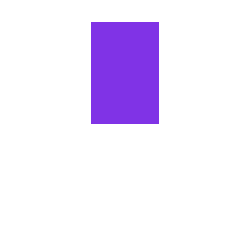
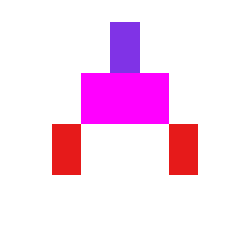
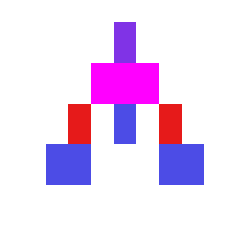
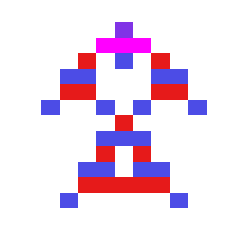
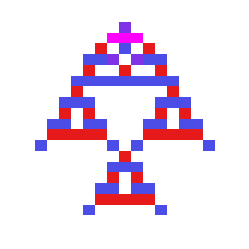
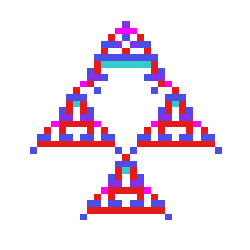
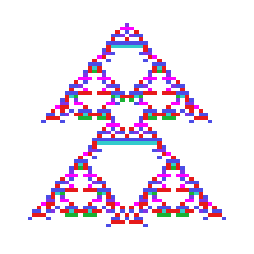
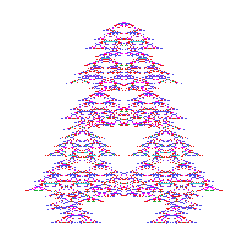
-Graphics-1-Graphics-3-Graphics-4-Graphics-12-Graphics-18-Graphics-30-Graphics-57-Graphics-746-Graphics-1835

```mathematica
Row[sequence[[All,1]]]
```

```mathematica
k=10;
r=10;
increment=.1;
sequence=Quiet[PoissonRandomWalkSearch[k,r,1,RuleLength[k,r],2000,increment]];
Row[sequence[[All,1]]]
```

-Graphics-

To increase the likelihood of discovering rules that produce longer-lasting lifeforms, it is recommended to use a λ increment smaller than 0.5. The following 3D plot shows the maximum lifetime achieved for each configuration. Although there are some instances where a larger increment led to good results, these cases are much less frequent and less probable overall.

```mathematica
Labeled[ListPointPlot3D[datapoints,Filling->Bottom,AxesLabel->{"k","increment","Max length"}],Style[Text["Max length by different increments and states (r = 1)"],12]]
```

-Graphics3D-Max length by different increments and states (r = 1)

### Poisson Random Walk Search

The Poisson distribution provides a dynamic and tunable mechanism for balancing exploration and exploitation in the rule space, helping the algorithm discover increasingly complex or stable patterns without getting trapped in early suboptimal choices. The PoissonRandomWalkSearch function works as follows:

Initialization: It begins with rule 0 and calculates its lifetime. This serves as the starting point of the search.

Neighbor Generation: For each iteration, it generates all possible single-digit mutations of the current rule in base k. These mutated rules form the set of neighbors.

Fitness Evaluation: It evaluates the lifetime of each neighbor using the TestCALifetime function and filters out any invalid or degenerate results.

Poisson-Based Selection: It applies a Poisson distribution (with increasing λ) to assign weights to neighbors based on their lifetimes. These weights are used to compute selection probabilities, favoring higher-lifetime rules more as λ grows.

Update and Record: The best rule found so far is updated whenever a new rule with a longer lifetime is discovered. That rule is stored using Sow, and λ is reduced temporarily to re-focus the search locally.

Termination: The loop continues until λ exceeds 5. The function then returns the sequence of best configurations found throughout the run.

This method is an efficient and adaptive way to navigate the vast rule space of cellular automata using a biologically inspired probabilistic model.

```mathematica
PoissonRandomWalkSearch[k_,r_,init_,ruleLength_,times_,increment_]:=Module[{currentRule=0,currentRuleDigits,currentLife,bestRule=0,bestLife=0,lambda=0.01,sequence},
currentRuleDigits=IntegerDigits[currentRule,k,ruleLength];
currentLife=TestCALifetime[CellularAutomaton[{currentRule,{k,1},r},{{init},0},times]];

(*Start the Poisson-driven random walk loop*)
sequence=Reap[While[lambda<3,lambda+=increment;
PrintTemporary["Increment: ",lambda," to 3 (",k,",",r,")"];
(*Convert rule to digit list*)
currentRuleDigits=IntegerDigits[currentRule,k,ruleLength];

(*Generate all single-mutation neighbors of the current rule*)
neighbourDigits=Flatten[Reap[Do[Do[
Sow[ReplacePart[currentRuleDigits,i->val]]
,{val,0,k-1}],{i,ruleLength-1}]][[2]],1]//DeleteDuplicates;

(*Convert digits back to rule numbers*)
neighbourRules=FromDigits[#,k]&/@neighbourDigits;

(*Get lifetimes for each neighbor*)
lifetimes=TestCALifetime[CellularAutomaton[{#,{k,1},r},{{init},0},times]]&/@neighbourRules;

(*Pair rules with lifetimes and sort by lifetime (descending)*)
validNeighbours=Select[Reverse@SortBy[Transpose[{neighbourRules,lifetimes}],Last],Not[MemberQ[{-Infinity},#[[2]]]]&];

(*Extract lifetimes for weighting*)
weights=validNeighbours[[All,2]];

(*Apply Poisson weighting based on lambda*)
poissonWeights=PDF[PoissonDistribution[lambda],#]&/@weights;
priority=1/poissonWeights;
probabilities=priority/Total[priority];

(*Pair rule,lifetime,and selection probability*)
rulePool=Transpose[{validNeighbours[[All,1]],weights,probabilities}];

(*Select a new rule using the calculated probabilities*)
{newRule,newLife,prob}=RandomChoice[rulePool[[All,3]]->rulePool];

(*Update the best rule found so far if improved*)
If[newLife>bestLife,bestRule=newRule;
bestLife=newLife;
Sow[{
Labeled[
If[IntegerQ[r],
DrawCA[CellularAutomaton[{bestRule,{k,1},r},{{init},0},bestLife],k],
SerratedBricksArrayPlot[CellularAutomaton[{bestRule,{k,1},r},{{init},0},bestLife]]],bestLife],
bestLife
}];
lambda/=2;];

(*Set current rule to the selected one*)
currentRule=newRule;
currentLife=newLife;]][[2]]//Flatten;

(*Return the collected sequence of best configurations*)
sequence=Partition[sequence,2];
sequence
]
```

## Concluding Remarks

This work explored the emergence of finite lifeforms in one-dimensional totalistic cellular automata, starting from a single active cell. By applying a series of logical filters, the number of rules to evaluate was drastically reduced, allowing a feasible brute-force search within small configurations.

Through this approach, a variety of finite patterns were discovered, and their distribution across the rule space was analyzed. The results showed that shorter lifeforms are more common and widely distributed, while longer lifeforms are rarer and more isolated in the rule space.

To better understand these relationships, we developed a graph-based exploration algorithm using a breadth-first strategy. This allowed us to group rules by behavior and reveal the connectivity between them through minimal mutations. The resulting graphs showed that rules producing similar finite lifeforms tend to form tightly connected clusters, while longer and more complex lifeforms appear at the periphery with fewer connections.

Overall, this methodology not only allowed the discovery of interesting finite patterns but also provided a framework to study the structure of the rule space, the robustness of lifeforms, and the evolutionary paths between different configurations.

## Acknowledgments

I would like to express my deep gratitude to my mentor Willem Nielsen for his constant support and guidance throughout this project. His patience, clarity, and deep understanding of the subject were fundamental to my progress. I am also thankful to Alejandra Ortiz and Hugo Suárez, who assisted me with the code and helped me overcome technical and style challenges during the development.

Special thanks to Stephen Wolfram for suggesting the project direction and finally, I want to thank Professor Genaro Juárez for giving me the opportunity to attend the WSS and present this work.

## Functions

### Animations

```mathematica
a=Table[Rasterize[Labeled[Grid[{{RulePlot[CellularAutomaton[{i,{2,1},1}],ColorRules->globalColorRules],ArrayPlot[CellularAutomaton[{i,{2,1},1},{0,0,0},4],Mesh->True,ColorRules->globalColorRules]}},Spacings->{2,2}],"Cellular Automaton: Rule "<>ToString[i]<>" (r=1, k=2)",Top],RasterSize->500],{i,1,15,2}];
Export["./img/spontaneous_life.gif",a,"DisplayDurations"->0.4];
```

```mathematica
rules=Select[Range[0,2186,3],Mod[#,9]==3&];

(*Generar frames rasterizados*)
frames=Table[Module[{r=rules[[i]]},Rasterize[Labeled[Grid[{{RulePlot[CellularAutomaton[{r,{3,1},1}],ColorRules->globalColorRules],ArrayPlot[CellularAutomaton[{r,{3,1},1},{{1},0},10],ColorRules->globalColorRules,Mesh->True]}},Spacings->{2,2}],"Cellular Automaton: Rule "<>ToString[r]<>" (r=1, k=3)",Top],RasterSize->500]],{i,Length[rules]}];

(*Exportar a GIF*)
Export["./img/spontaneous_life_k3.gif",frames,"DisplayDurations"->0.4];
```

```mathematica
(*Parameters*)
from=0;
to=2186;
init=1;
k=3;
r=1;

(*Selección de reglas*)
rules=Select[Range[from,to,k],Mod[#,k^2]!=init*k&];

(*Filtro de reglas*)
filteredRules=Reap[Do[result=CellularAutomaton[{rule,{k,1},r},{{init},0},1];
If[Length[result[[2]]]==1&&result[[2,1]]==0,Sow[rule,"rule"]],{rule,rules}],{"rule"}][[2,1]]//Flatten;

(*Generar y rasterizar los frames*)
frames=Table[Module[{rule=filteredRules[[i]]},Rasterize[Labeled[Grid[{{RulePlot[CellularAutomaton[{rule,{k,1},r}],ColorRules->globalColorRules],ArrayPlot[CellularAutomaton[{rule,{k,1},r},{{init},0},3],ColorRules->globalColorRules,Mesh->True]}},Spacings->{2,2}],"Celular Automaton: Rule "<>ToString[rule]<>" (r="<>ToString[r]<>", k="<>ToString[k]<>")",Top],RasterSize->500]],{i,Length[filteredRules]}];

(*Exportar GIF*)
Export["./img/filtered_rules_k"<>ToString[k]<>"_r"<>ToString[r]<>".gif",frames,"DisplayDurations"->0.4];
```

### Manual execution

```mathematica
(*Code to generate config rules*)
times=700;
configRules=Table[
Table[
definedRules=defineRules[config["k"],config["r"],times,init,0,config["rules"]];

(*Apply TestCALifetime to identify those rules with finite lifeform*)
lts=ParallelMap[
{#,
TestCALifetime[
CellularAutomaton[{#,{config["k"],1},config["r"]},{{init},0},times]
]
}&,definedRules];

finiteRules=Select[lts,(#[[2]]!=-Infinity&)];

(*Group rules by the same lifeform*)
groupRules=SimilarTCA[finiteRules,config["k"],config["r"],init,(2*config["r"]+1)*(config["k"]-1)+1];
groupRules=SortBy[groupRules,(#[["length"]]&)];

config=Append[config,"init"->init];
config=Append[config,"groups"->groupRules];
config

,{init,config["k"]-1}]
,{config,configurations}]//Flatten;

Iconize[configRules]
```

```mathematica
(*Datapoints for test max left in different configurations*)
datapoints=Table[
ParallelTable[
{k,i,Max[Quiet[PoissonRandomWalkSearch[k,r,1,RuleLength[k,r],times,i]][[All,2]]]}
,{k,3,10}]
,{i,0.1,1.0,.1}];
```

### Search and group functions

```mathematica
TestCALifetime[ca_List]:= If[#==0,-Infinity,Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#]==0&]]
```

```mathematica
defineRules[k_,r_,times_,init_,from_,to_]:=Module[{
length=k^((2r+1)(k-1)+1)-1,
numRules,
result},
(*Only use multiples of 'k' to avoid spontaneous live*)
(*If the second gene equals the init, it grows to infinite*)
numRules=Select[Range[from,to,k],(Mod[#,k^2]-init k!=0&)];

(*If the second line is empty, it deaths*)
numRules=Reap[Do[
result=CellularAutomaton[{rule,{k,1},r},{{init},0},2];
If[Length[result[[2]]]!=1||result[[2,1]]!=0,
Sow[rule,"rule"]],{rule,numRules}],{"rule"}][[2,1]]//Flatten;
numRules
];
times=700;
```

```mathematica
SimilarTCA[finiteRules_,k_,r_,init_,ruleLength_]:=Module[{sameLength},
sameLength=GroupBy[finiteRules,Last][[All,All,1]];

(*Iterate all the sameLenght rules*)
data=Reap[Do[
evolutions=Map[{#,CellularAutomaton[{#,{k,1},r},{{init},0},key-1]}&,sameLength[key]];
lifeforms=GatherBy[evolutions,#[[2]]&];
Sow[{key,#[[All,1]]&/@lifeforms},"evo"];
,{key,Keys[sameLength]}],{"evo"}][[2,1,1]];

Table[
(<|"length"->i[[1]],
"rules"->#,
"rule"->Table[
If[SameQ@@col,First[col],"x"],{col,Transpose[
Table[IntegerDigits[i,k,ruleLength],{i,#}]]}]|>&/@i[[2]])
,{i,data}]//Flatten
]
```

```mathematica
RuleLength[k_,r_]:=(2*r+1)*(k-1)+1
```

```mathematica
CalculateDifference[list1_,list2_]:=Count[MapThread[#1=!=#2&&#1=!="x"&&#2=!="x"&,{list1,list2}],True]
```

### Plot functions

```mathematica
globalColorRules={0->RGBColor[1,1,1],1->RGBColor[0.5,0.2,0.9],2->RGBColor[1,0,1],3->RGBColor[0.1,0.6,1],4->RGBColor[1,0.6,0.1],5->RGBColor[0.1,0.7,0.2],6->RGBColor[0.9,0.1,0.1],7->RGBColor[0.3,0.3,0.9],8->RGBColor[0.2,0.8,0.8],9->RGBColor[0.9,0.5,0.2],10->RGBColor[0.7,0.2,0.7],11->RGBColor[0.2,0.9,0.3],12->RGBColor[0.9,0.2,0.5],13->RGBColor[0.4,0.6,0.1],14->RGBColor[0.6,0.4,0.9]};
```

```mathematica
PlotConfigRules[configRules_,pos_]:=Module[{k,r,init,ruleL},

k=configRules[[All,"k"]][[i]];
r=configRules[[All,"r"]][[i]];
init=configRules[[All,"init"]][[i]];
ruleL=RuleLength[k,r];
DrawLife[configRules[[i,"groups"]],ruleL,k,r,init]]
```

```mathematica
DrawLife[rules_,length_,k_,r_,init_]:=
Table[
integerRules=IntegerDigits[#,k,length]&/@rules[[rule,"rules"]];

newRule=Table[If[SameQ@@col,First[col],"x"],{col,Transpose[integerRules]}];
Labeled[
If[IntegerQ[r],
DrawCA[CellularAutomaton[{rules[[rule,"rules",1]],{k,1},r},{{init},0},rules[[rule,"length"]]],k],
SerratedBricksArrayPlot[CellularAutomaton[{rules[[rule,"rules",1]],{k,1},r},{{init},0},rules[[rule,"length"]]]]
]
,"Rule: "<>ToString[newRule]<>"\nLength: "<>ToString[rules[[rule,"length"]]]<>"\nSimilar rules: "<>ToString[Length[rules[[rule,"rules"]]]]<>"\nk: "<>ToString[k]<>"\nr: "<>ToString[r//N]<>"\ninit: "<>ToString[init],Right]
,{rule,1,Length[rules],1}]
```

```mathematica
DrawCA[data_,states_]:=
ArrayPlot[ArrayPad[#,1]&/@data,
ColorRules->globalColorRules,
ImageSize->{300,300}
(*ImageSize->30 Sqrt[TestCALifetime[data]]*)]
```

```mathematica
Draw3D[groupRules_]:=Module[{vertex,edges,graph,embed,graph3d, coordinates, stylizedVertices, max},(*Generate the vertices,edges and the graph*)vertex=Table[x,{x,groupRules[[All,"rule"]]}];
edges=Table[If[CalculateDifference[vertex[[i]],vertex[[j]]]==1,UndirectedEdge[vertex[[i]],vertex[[j]]],Nothing],{i,Length[vertex]},{j,i+1,Length[vertex]}]//Flatten;
graph=Graph[edges,VertexWeight->(#["rule"]->#["length"]&/@groupRules)];
(*Reorder emmbedings to have the same order of the edges*)Flatten[Position[groupRules[[;;,"rule"]],#]&/@VertexList[edges]];
embed=groupRules[[Flatten[Position[groupRules[[;;,"rule"]],#]&/@VertexList[edges]]]];
coordinates= Thread[embed[[All,"rule"]]->Transpose[Append[Transpose[GraphEmbedding[edges]*(Length[groupRules]/100+Log[Length[groupRules]])],embed[[All,"length"]]/. Thread[Sort[DeleteDuplicates[embed[[All,"length"]][[Flatten[Position[embed[[All,"rule"]],#]&/@VertexList[edges]]]]]]->Range[Length[DeleteDuplicates[embed[[All,"length"]][[Flatten[Position[embed[[All,"rule"]],#]&/@VertexList[edges]]]]]]]]]]];
max=Max[coordinates[[All,2]][[All, 3]]];
stylizedVertices = coordinates/.(HoldPattern[vertex:{__}->coordinate:{_,_,height_}]:>vertex->Hue[height/max]);


(*Plot3D,taking the actual lenght as hight*)
graph3d=GraphPlot3D[EdgeList[graph],
VertexCoordinates->coordinates,
Boxed->True,
Axes->True,
EdgeShapeFunction->(Cylinder[#1,.015]&),
VertexStyle->stylizedVertices,
VertexSize->(Log[Length[groupRules]])Log[Length[groupRules],10]-((Log[Length[groupRules],10])Log[Length[groupRules],10])-1,
ViewPoint->{0,-3,0}

(*VertexLabels->Thread[embed[[All,"rule"]]->embed[[All,"length"]]]*)];
Print[graph3d];
graph
]
```

```mathematica
SerratedBricksArrayPlot[d_, opts:OptionsPattern[{Graphics}]] := Module[
{paddedData, grps, keymax,
data=ArrayPad[#,3]&/@d},
	paddedData =CropMatrixColumns[
MapThread[Function[Join[ConstantArray[0, Floor[#2 / 2]], #]],
			{
				MapThread[
					Function[Join[#, ConstantArray[0, Ceiling[#2 / 2]]]],
					{data, Range[0, Length[data] - 1]}
				],
				If[Divisible[Length @ data, 2],
					Range[Length @ data, 1, -1],
					Range[Length[data] - 1, 0, -1]
				]
			}
		]
	];
	grps = KeySort[
		GroupBy[
			Catenate[
				MapIndexed[
					Function[
						# -> (Reverse[#2 * {-1, 1}] - Mod[Part[#2, 1], 2] * {1 / 2, 0})
					],
					paddedData, {2}
				]
			],
			First -> Last
		]
	];
	keymax = Last @ Keys @ grps;
	Graphics[
		KeyValueMap[Function@{EdgeForm[None],#/. globalColorRules,Map[Rectangle,#2]},grps],
		opts
	]
];
CropMatrixColumns[mat_ ? MatrixQ, Optional[pad_, 3]] := With[
	{h = Part[Dimensions @ mat, 2]},
	Take[mat,
		All,
		Apply[Function @ {Max[#, 1], Min[#2, h]},
			MinMax[Part[ArrayRules[mat], 1;;-2, 1, 2]] + pad * {-1, 1}
		]
	]
];
```

### Graph functions

```mathematica
ClassifyNeighbourRules[rule_,k_,r_]:=Module[{
mutated=MutateRule[rule,RuleLength[k,r],k],
zero, infinite, finite
},

mutated=Transpose[{mutated,TestCALifetime[CellularAutomaton[{#,{k,1},r},{{init},0},times]]&/@mutated}];

{zero,infinite,finite}=Reap[
Do[
Which[
m[[2]]==1,Sow[m[[1]],"zero"],
m[[2]]==-∞||m[[2]]==times,Sow[m[[1]],"infinite"],
m[[1]]!=rule,Sow[m,"finite"]
];
,{m,mutated}]
,{"zero","infinite","finite"}][[2]];
{zero//Flatten,infinite//Flatten,finite[[1]]}
]
```

```mathematica
MutateRule[rule_,length_,k_]:=Module[{digits,mutated},
digits=IntegerDigits[rule,k,length];
mutated=Reap[Do[Do[
Sow[ReplacePart[digits,i->j]]
,{j,0,k-1}],{i,length-1}]
][[2,1]]//DeleteDuplicates;
FromDigits[#,k]&/@mutated
]
```

False

## References

E. Weisstein (n.d.), “Cellular Automaton,” MathWorld – A Wolfram Web Resource. https://mathworld.wolfram.com/CellularAutomaton.html

E. Weisstein (n.d.), “Totalistic Cellular Automaton,” MathWorld – A Wolfram Web Resource. https://mathworld.wolfram.com/TotalisticCellularAutomaton.html

S. Wolfram (2024), “Why Does Biological Evolution Work? A Minimal Model for Biological Evolution and Other Adaptive Processes,” Stephen Wolfram Writings. https://writings.stephenwolfram.com/2024/05/why-does-biological-evolution-work-a-minimal-model-for-biological-evolution-and-other-adaptive-processes

J. Hurtado et al. (2024), “Exploring Finite Lifeforms in Totalistic Cellular Automata,” Wolfram Community Post. https://community.wolfram.com/groups/-/m/t/3208800

## Cite This Notebook

Adaptative Evolution in Totalistic Cellular Automaton
by Erick Jesse Angeles Lopez
Wolfram Community, STAFF PICKS, July 9, 2025
https://community.wolfram.com/groups/-/m/t/3496929